```mathematica
dir="ownCloud/EMORY/bia_j/resdump/syn_varios/";
m01=Import[dir<>"synthetic_T20_Nmax500mJ05_mlevel_id901.dat","Table"];
m02=Import[dir<>"synthetic_T20_Nmax500mJ05_mlevel_id902.dat","Table"];
Dimensions /@ {m01,m02}
m01[[{1,40},;;4]]
<<MaTeX`
```

{{42,16},{42,16}}

{{2,200,0.5,500},{4,1600,0.5,500}}

{0.02,0.04,0.08,0.16,0.32,0.64,1.28,2.56,5.12,10.24,20.48,40.96}

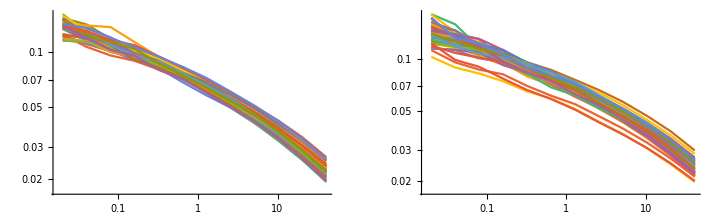

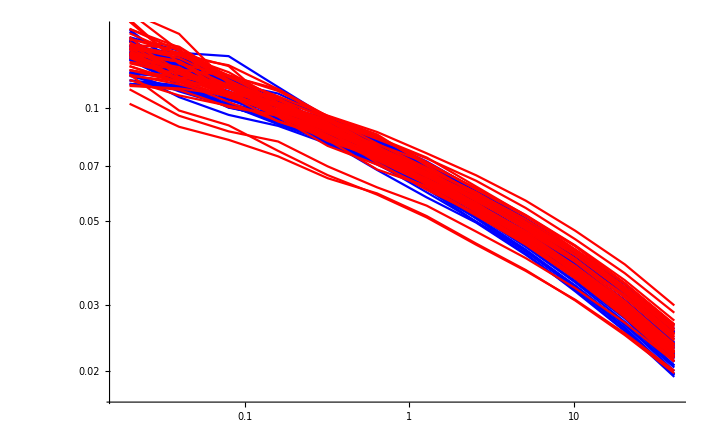

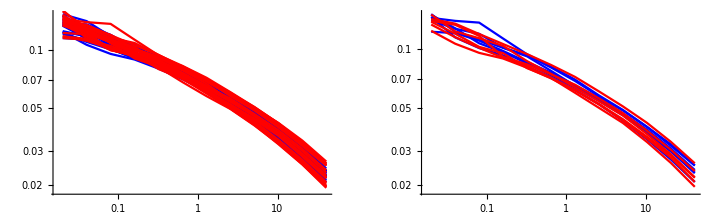

```mathematica
nf=Table[0.02 2^(i-1),{i,12}]
GraphicsRow[{ListLogLogPlot[Transpose@{nf,#}& /@m01[[All,5;;]],Joined->True],
ListLogLogPlot[Transpose@{nf,#}& /@m02[[All,5;;]],Joined->True]}]
Show[ListLogLogPlot[Transpose@{nf,#}& /@m01[[All,5;;]],Joined->True,PlotStyle->Blue],
ListLogLogPlot[Transpose@{nf,#}& /@m02[[All,5;;]],Joined->True,PlotStyle->Red]]
GraphicsRow[{Show[ListLogLogPlot[Transpose@{nf,#}& /@Select[m01,#[[1]]==2&][[All,5;;]],Joined->True,PlotStyle->Blue],
ListLogLogPlot[Transpose@{nf,#}& /@Select[m01,#[[1]]==4&][[All,5;;]],Joined->True,PlotStyle->Red]],
Show[ListLogLogPlot[Transpose@{nf,#}& /@Select[m01,#[[2]]==200&][[All,5;;]],Joined->True,PlotStyle->Blue],
ListLogLogPlot[Transpose@{nf,#}& /@Select[m01,#[[2]]==1600&][[All,5;;]],Joined->True,PlotStyle->Red]]}]
```

```mathematica
m01[[All,;;4]]
```

{{2,200,0.5,500},{2,200,0.5,500},{2,200,0.5,500},{2,283,0.5,500},{2,283,0.5,500},{2,283,0.5,500},{2,400,0.5,500},{2,400,0.5,500},{2,400,0.5,500},{2,566,0.5,500},{2,566,0.5,500},{2,566,0.5,500},{2,800,0.5,500},{2,800,0.5,500},{2,800,0.5,500},{2,1131,0.5,500},{2,1131,0.5,500},{2,1131,0.5,500},{2,1600,0.5,500},{2,1600,0.5,500},{4,200,0.5,500},{4,200,0.5,500},{4,283,0.5,500},{4,283,0.5,500},{4,400,0.5,500},{2,1600,0.5,500},{4,400,0.5,500},{4,200,0.5,500},{4,566,0.5,500},{4,566,0.5,500},{4,283,0.5,500},{4,800,0.5,500},{4,800,0.5,500},{4,400,0.5,500},{4,566,0.5,500},{4,1131,0.5,500},{4,1131,0.5,500},{4,800,0.5,500},{4,1600,0.5,500},{4,1600,0.5,500},{4,1131,0.5,500},{4,1600,0.5,500}}

{84,12,2}

{{0.02,0.138992},{0.04,0.124754},{0.08,0.110978},{0.16,0.0984005},{0.32,0.086756},{0.64,0.075522},{1.28,0.06502},{2.56,0.0551687},{5.12,0.0461523},{10.24,0.0377639},{20.48,0.0300835},{40.96,0.0232154}}

FittedModel[-2.67734-0.231535 x-0.0145036 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.0145036 | 0.000958852 | -15.126 | 1.04904×10^-7
b | -0.231535 | 0.00203945 | -113.528 | 1.62068×10^-15
c | -2.67734 | 0.0073266 | -365.427 | 4.38067×10^-20

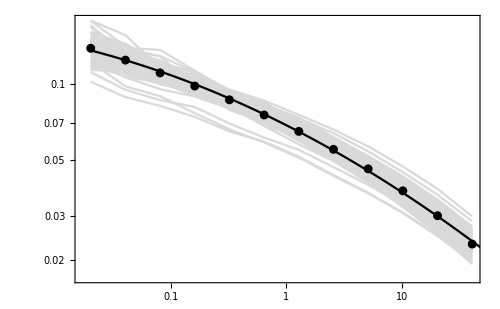

```mathematica
all=Transpose@{nf,#}& /@(m01[[All,5;;]]~Join~m02[[All,5;;]]);
Dimensions @all
mall=Mean@all
(*f=Interpolation[Log @mall];
Show[LogLogPlot[Exp@f[Log@x],{x,0.02,50}],ListLogLogPlot[mall]]*)
nlm=NonlinearModelFit[Log@mall,a x^2+b x+c,{a,b,c},x]
(*Show[ListLogLogPlot[mall],LogLogPlot[Exp@nlm[Log@x],{x,0.02,50}]]*)
nlm["ParameterTable"]
font=18;
figmnf=Show[ListLogLogPlot[#,Joined->True,PlotStyle->LightGray,Frame->True,FrameStyle->Directive[font],FrameTicks->{{Automatic,None},{{0.1,1,10},None}},ImageSize->500,FrameLabel->{MaTeX["n \\text{ [number of patterns above threshold]}",FontSize->font+2],MaTeX["m \\text{ [threshold for magnetization]}",FontSize->font+2]},Epilog->Inset[MaTeX["\\log m= \\log \\left[ m(1) n^{-0.23} \\right]- 0.015 (\\log n)^2",FontSize->font],Scaled[{.4,.15}]]]&@all,ListLogLogPlot[mall(*,Joined->True*),PlotStyle->{Black,Thick},Mesh->All],LogLogPlot[Exp@nlm[Log@x],{x,0.02,50},PlotStyle->Black]]
```

```mathematica
Export["ownCloud/EMORY/bia_j/figures/may2017_mlevel_nf/fig1.pdf",figmnf]
```

ownCloud/EMORY/bia_j/figures/may2017_mlevel_nf/fig1.pdf

## log m = -2.7 - 0.23 log n -0.015 (log n)^2, for mean log m = - c - 0.23 log n -0.015 (log n)^2, in general m = e^-c - n^-0.23 - e^(-0.015 (log n)^2), with c= -log m(1)

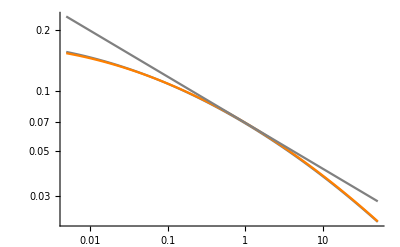

```mathematica
(*LogLogPlot[Exp@nlm[Log@x],{x,0.005,50}]*)
m1=Exp[-2.67];LogLogPlot[{Exp@nlm[Log@x],m1 x^(-0.23)Exp[-0.015 (Log[x]^2)],m1 x^(-0.23)},{x,0.005,50},PlotStyle->{Gray,Orange}]
```

## Testing formula (sort of, when you know exactly m[1.28])

```mathematica
mc[x_,m1_:Exp[-2.67]]:=m1 x^(-0.23)Exp[-0.015 (Log[x]^2)]
```

```mathematica
nf
nf[[7]]
c0=(1.28)^(-0.23)Exp[-0.015 (Log[1.28]^2)]
```

{0.02,0.04,0.08,0.16,0.32,0.64,1.28,2.56,5.12,10.24,20.48,40.96}

1.28

0.943941

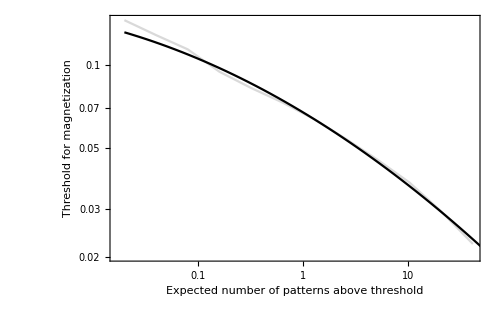

```mathematica
i=14;
Show[ListLogLogPlot[all[[i]],Joined->True,PlotStyle->LightGray,Frame->True,FrameStyle->Directive[20],FrameTicks->{{Automatic,None},{{0.1,1,10},None}},ImageSize->500,FrameLabel->{"Expected number of patterns above threshold","Threshold for magnetization"},Epilog->Inset[MaTeX["\\log m= \\log \\left[ m(1) n^{-0.23} \\right]- 0.015 (\\log n)^2",FontSize->18](*,{0.02,Center}*)]],LogLogPlot[(*Exp@nlm[Log@x]*)mc[x,all[[i,7,2]]/c0],{x,0.02,50},PlotStyle->Black]]
```

```mathematica
nf2=Table[0.005 Sqrt[2]^(i-1),{i,27}]
mc[#,Exp[-2.67]]& /@ nf2
```

{0.005,0.00707107,0.01,0.0141421,0.02,0.0282843,0.04,0.0565685,0.08,0.113137,0.16,0.226274,0.32,0.452548,0.64,0.905097,1.28,1.81019,2.56,3.62039,5.12,7.24077,10.24,14.4815,20.48,28.9631,40.96}

{0.153744,0.149734,0.145304,0.140499,0.135363,0.129946,0.124298,0.118467,0.112503,0.106456,0.100371,0.0942936,0.0882656,0.0823257,0.0765094,0.0708482,0.06537,0.0600984,0.0550532,0.0502501,0.0457011,0.0414144,0.0373948,0.0336438,0.0301603,0.0269402,0.0239773}

```mathematica
Round @Table[200. Sqrt[2]^(i-1),{i,7}]
```

{200,283,400,566,800,1131,1600}